```mathematica
MeanFieldNoCompet[input_,initial_]:=Module[{b,ns,nstep,T,w,a,muR=0.1,qS=0.5,nu,step,Q,rho,initialE,initialO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution,tempResult,Result},
ns=input[[1]];
b=input[[2]];
If[b==0,Result={0,0};Goto[end]];
nstep=input[[3]];
T=input[[4]];
w=input[[5]];
a = input[[6]];
step=1/nstep;
nu=If[ns≠0,w/(ns)^2];
Q=Range[0+step,1,step];

(*a=If[ns==0,0.4,0.5];*)

Fitness[q_]:=If [ns==0,1. ,Exp[1/nu*  Cos[2 Pi q- 2 Pi qS]]/( BesselI[0,1/nu])];

If[Length[initial]==0,
initialE= Table[rho[q,0][0]==0.5*b/muR,{q,Q}];
initialO= Table[rho[q,1][0]==0.5*b/muR,{q,Q}],
initialE= Table[rho[Q[[i]],0][0]==initial[[i,1]],{i,Length@Q}];
initialO= Table[rho[Q[[i]],1][0]==initial[[i,2]],{i,Length@Q}];
];

fE[q_,t_]:= b- muR* rho[q,0][t]- rho[q,0][t]* a*Fitness[q]* Sum[step*rho[qq,1][t],{qq,Q}];
fO[q_,t_]:=-muR *rho[q,1][t]+rho[q,0][t]* a*Fitness[q]* Sum[step*rho[qq,1][t],{qq,Q}];

systemE=Table[rho[q,0]'[t]==fE[q,t],{q,Q}];
systemO=Table[rho[q,1]'[t]==fO[q,t],{q,Q}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[rho[qq,0],{qq,Q}];
variableO=Table[rho[qq,1],{qq,Q}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,T}];

tempResult=Flatten[Evaluate[Table[{rho[q,0][T],rho[q,1][T]},{q,Q}] /.Solution],1];

Result=step*Total[tempResult];
Label[end];
{Result,tempResult}];
```

```mathematica
(*use this for exploring niche width and colonization rate parameter*)
NoCompetModel2[input_]:=
Module[{b,ns,w,aa,in, difference,time,eps=10^(-7),(*totalresult={},*)nstep=200,finalresult={},lastresult,newresult,diff,epscheck,tresult,rawresult,initial},
ns=input[[1]];
aa = input[[2]];
Do[
b =2.;
time=1000;
lastresult={0,0};initial={};
difference=True;
in = {ns,b,nstep,time,w,aa};
While[difference==True,
rawresult=Chop[MeanFieldNoCompet[in ,initial]];
newresult=rawresult[[1]];
initial=rawresult[[2]];
(*AppendTo[totalresult,newresult];*)
diff=Abs[newresult-lastresult];
If[diff[[1]]<eps&&diff[[2]]<eps,difference=False];
lastresult=newresult;
time+=5000;
If[time>10^7,newresult={1000,1};Goto[leave]];
];
Label[leave];
AppendTo[finalresult,{w,newresult[[2]]/Total[newresult]}];
,{w,Flatten[{Range[0.01,0.1,0.01],Range[0.2,10,0.2],20}]}];
Export[StringJoin["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure2\\Panel abc\\Fig2a_ns_" ,ToString[ns],"_a_",ToString[aa],"_nstep_",ToString@nstep,"_b_",ToString@b,".csv"],finalresult];
];
```

```mathematica
PARAM1=Flatten[Table[{ns,a},{ns,{4}},{a, {0.25,2}}],1];
AbsoluteTiming[ParallelMap[NoCompetModel2,PARAM1]];
```

### Figure 2a

```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure2\\";
```

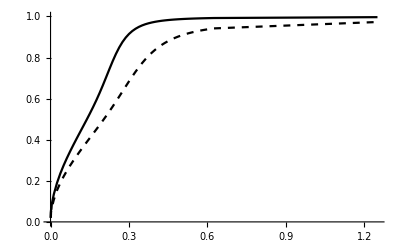

```mathematica
(*Plot*)
th = 1.5; fs  =24;pms = 16;
as = Directive[AbsoluteThickness[th],fs,Black,FontFamily->"Arial"];

ns = 4;data= {};Do[dt = Import[StringJoin[localdir,"Panel abc\\no_compet_ns_" ,ToString[ns],"_a_",ToString[aa],".csv"]];
dt[[All,1]] = dt[[All,1]] /ns^2; (*convert w to nu*)
AppendTo[data, dt];
,{aa, {2(*,0.5,1*),0.25}}];
fig2a = ListPlot[data, PlotRange-> {{0,5/4},{0,1}},PlotStyle-> {Black,{Black,Dashed}},AxesStyle-> as2,Joined->True,PlotRangePadding->{{0,0},{0,0.025}}]
```

```mathematica
Export[localdir<>"fig2a.jpeg",fig2a,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\fig2a.jpeg